```mathematica
c[x_,y_,n_]:={GrayLevel[1],Disk[{x,y},.3],GrayLevel[0],Circle[{x,y},.3]}
```

```mathematica
s[x_,y_,n_]:={GrayLevel[1],Rectangle[{x-.25,y-.25},{x+.25,y+.25}],GrayLevel[0],Line[{{x-.25,y-.25},{x-.25,y+.25},{x+.25,y+.25},{x+.25,y-.25},{x-.25,y-.25}}]}
```

```mathematica
t[x_,y_,n_]:={GrayLevel[1],Polygon[{{x-.35,y-.2},{x+.35,y-.2},{x,y-.2+.35Sqrt[3]}}],GrayLevel[0],Line[{{x-.35,y-.2},{x+.35,y-.2},{x,y-.2+.35Sqrt[3]},{x-.35,y-.2}}]}
```

```mathematica
p[x_,y_,n_]:={GrayLevel[1],Polygon[Table[{x+.33Cos[2Pi i/5+Pi/10],y+.33Sin[2Pi i/5+Pi/10]},{i,1,5}]],GrayLevel[0],Line[Table[{x+.33Cos[2Pi i/5+Pi/10],y+.33Sin[2Pi i/5+Pi/10]},{i,0,5}]]}
```

```mathematica
h[x_,y_,n_]:={GrayLevel[1],Polygon[Table[{x+.33Cos[2Pi i/6],y+.33Sin[2Pi i/6]},{i,1,6}]],GrayLevel[0],Line[Table[{x+.33Cos[2Pi i/6],y+.33Sin[2Pi i/6]},{i,0,6}]]}
```

```mathematica
c[x_,y_,n_]:={GrayLevel[1],Disk[{x,y},.3],GrayLevel[0],Circle[{x,y},.3],Text[Style[n,FontFamily->"Times",FontSize->20],{x,y}]}
```

```mathematica
s[x_,y_,n_]:={GrayLevel[1],Rectangle[{x-.25,y-.25},{x+.25,y+.25}],GrayLevel[0],Line[{{x-.25,y-.25},{x-.25,y+.25},{x+.25,y+.25},{x+.25,y-.25},{x-.25,y-.25}}],Text[Style[n,FontFamily->"Times",FontSize->20],{x,y}]}
```

```mathematica
t[x_,y_,n_]:={GrayLevel[1],Polygon[{{x-.35,y-.2},{x+.35,y-.2},{x,y-.2+.35Sqrt[3]}}],GrayLevel[0],Line[{{x-.35,y-.2},{x+.35,y-.2},{x,y-.2+.35Sqrt[3]},{x-.35,y-.2}}],Text[Style[n,FontFamily->"Times",FontSize->20],{x,y}]}
```

```mathematica
p[x_,y_,n_]:={GrayLevel[1],Polygon[Table[{x+.33Cos[2Pi i/5+Pi/10],y+.33Sin[2Pi i/5+Pi/10]},{i,1,5}]],GrayLevel[0],Line[Table[{x+.33Cos[2Pi i/5+Pi/10],y+.33Sin[2Pi i/5+Pi/10]},{i,0,5}]],Text[Style[n,FontFamily->"Times",FontSize->20],{x,y}]}
```

```mathematica
h[x_,y_,n_]:={GrayLevel[1],Polygon[Table[{x+.33Cos[2Pi i/6],y+.33Sin[2Pi i/6]},{i,1,6}]],GrayLevel[0],Line[Table[{x+.33Cos[2Pi i/6],y+.33Sin[2Pi i/6]},{i,0,6}]],Text[Style[n,FontFamily->"Times",FontSize->20],{x,y}]}
```

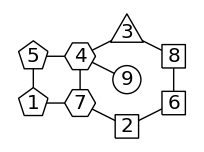

```mathematica
Show[Graphics[{Line[{{3,1.5},{2,2},{1,2},{1,1},{2,1},{3,0.5},{4,1},{4,2},{3,2.5},{2,2},{2,1}}],p[1,1,1],p[1,2,5],h[2,1,7],h[2,2,4],s[3,0.5,2],c[3,1.5,9],t[3,2.5,3],s[4,1,6],s[4,2,8]}],AspectRatio->Automatic]
```

```mathematica
Show[Graphics[{Line[{{1,1},{4,1},{5,1.5},{4,2},{1,2}}],c[1,1,4],t[2,1,2],h[3,1,5],h[4,1,3],s[5,1.5,8],s[4,2,6],h[3,2,7],p[2,2,1],c[1,2,9]}],AspectRatio->Automatic]
```

```mathematica
Show[Graphics[{Line[{{2,3},{1,2},{2,1},{2,3},{5,3},{7,2},{5,1},{6,2},{5,3},{4,2},{5,1},{3,2},{5,3},{5,1},{2,1}}],c[1,2,8],t[2,1,5],h[2,3,9],p[3,2,1],t[4,2,4],t[5,1,7],h[5,3,6],s[6,2,2],h[7,2,3]}],AspectRatio->Automatic]
```

```mathematica
Show[Graphics[{Line[{{2,1},{1,1},{1,2},{2,2},{3,1.5},{4,1},{5,1},{5,2},{4,2},{3,1.5}}],c[2,1,4],p[1,1,5],p[1,2,1],p[2,2,3],p[3,1.5,2],p[4,1,8],s[5,1,6],c[5,2,7],p[4,2,9]}],AspectRatio->Automatic]
```

```mathematica
Show[Graphics[{Line[{{2,1},{2,2},{1,2},{1,1},{5,1},{5,2},{4,2},{4,1},{5,2}}],t[1,2,8],t[2,2,2],s[1,1,4],h[2,1,3],s[3,1,7],h[4,1,9],p[5,1,1],t[4,2,5],c[5,2,6]}],AspectRatio->Automatic]
```

```mathematica
Show[Graphics[{Line[{{5,1},{6,2},{5,3},{5,1},{1,1},{2,2},{1,3},{3,3},{3,1},{4,2},{3,3},{5,3}}],t[2,2,1],t[4,2,8],t[6,2,6],h[1,3,3],h[3,3,8],h[5,3,7],h[1,1,5],h[3,1,4],c[5,1,9]}],AspectRatio->Automatic]
```

```mathematica
Show[Graphics[{Line[{{2,3},{0,2},{2,0},{4,2},{0,2},{4,2},{2,3},{2,2},{0,0},{4,0},{2,2}}],c[0,0,8],c[2,0,2],s[4,0,9],c[1,1,4],s[3,1,7],c[2,2,5],c[0,2,6],c[4,2,1],c[2,3,3]}],AspectRatio->Automatic]
```

```mathematica
Show[Graphics[{Line[{{2,3},{0,2},{2,0},{4,2},{0,2},{4,2},{2,3},{2,2},{0,0},{4,0},{2,2}}],c[0,0,8],c[2,0,2],s[4,0,9],c[1,1,4],s[3,1,7],c[2,2,5],c[0,2,6],c[4,2,1],c[2,3,3]}],AspectRatio->Automatic]
```

```mathematica
Show[Graphics[{Line[{{0,0},{3,0},{4,0.5},{3,1},{2,1},{2,0},{2,1},{0,1},{0,0}}],t[0,0,2],t[0,1,6],t[1,1,3],s[1,0,4],h[2,0,7],c[2,1,5],c[3,1,9],h[3,0,8],p[4,1/2,1]}],AspectRatio->Automatic]
```

```mathematica
Show[Graphics[{Line[{{1,0},{1,1},{4,1},{4,0},{0,0}}],c[0,0,6],c[1,1,3],h[1,0,4],h[2,0,5],t[2,1,2],h[3,1,9],p[3,0,1],h[4,0,8],t[4,1,7]}],AspectRatio->Automatic]
```

```mathematica
Show[Graphics[{Line[{{-0.45,1},{-1,0.45},{1,-0.45},{0.45,-1},{-0.45,1}}],Line[{{0.45,-1},{-0.45,-1},{-1,-0.45},{1,0.45},{0.45,1},{-0.45,-1}}],t[0,0,6],c[-1,0.45,4],t[-0.45,1,2],p[0.45,1,1],h[1,0.45,7],s[-1,-0.45,8],h[-0.45,-1,3],t[0.45,-1,9],t[1,-0.45,5]}],AspectRatio->Automatic]
```

```mathematica
Show[Graphics[{Line[{{1,1},{0,0},{0,2},{1,1},{2,1},{0,0},{2,1},{0,2},{2,1},{3,1},{4,2},{5,1},{5,0},{4,0},{5,1},{4,0},{3,1}}],t[0,0,3],s[0,2,4],h[1,1,8],c[2,1,1],h[3,1,9],c[4,2,6],h[5,1,5],p[5,0,7],p[4,0,2]}],AspectRatio->Automatic]
```

```mathematica
Show[Graphics[{Line[{{1/2,1},{1,0},{1.5,1},{2,0},{0,0},{1/2,1},{3.5,1},{2.5,1},{3,0},{3.5,1},{4,0},{3,0}}],t[0,0,4],t[1,0,6],t[2,0,1],h[3,0,7],t[4,0,3],s[0.5,1,8],s[1.5,1,2],c[2.5,1,9],c[3.5,1,5]}],AspectRatio->Automatic]
```

```mathematica
Show[Graphics[{Line[{{1/2,1},{1,0},{1.5,1},{2,0},{0,0},{1/2,1},{3.5,1},{2.5,1},{2,0},{2.5,1},{3,0},{4,0}}],p[0,0,3],p[1,0,2],t[2,0,9],t[3,0,4],c[4,0,7],p[0.5,1,1],s[1.5,1,8],h[2.5,1,6],c[3.5,1,5]}],AspectRatio->Automatic]
```

```mathematica
Show[Graphics[{Line[{{0,0},{2,0},{2,2},{0,2},{0,0},{0,1},{2,1},{1,1},{1,2},{1,0}}],h[0,2,2],h[1,2,8],p[2,2,1],h[0,1,4],t[1,1,5],c[2,1,6],h[0,0,7],t[1,0,3],t[2,0,9]}],AspectRatio->Automatic]
```

```mathematica
Show[Graphics[{Line[{{0,0},{3,0},{1.5,3},{1,2},{2,2},{1,2},{0,0}}],Line[{{0.5,1},{1,0},{2.5,1},{2,0}}],t[1.5,3,1],t[1,2,2],s[2,2,8],h[0.5,1,3],t[2.5,1,9],h[0,0,7],s[1,0,4],c[2,0,6],h[3,0,5]}],AspectRatio->Automatic]
```

```mathematica
Show[Graphics[{Line[{{0,0},{1,0},{1/2,Sqrt[3]/2},{0,0}}],h[1/2,Sqrt[3]/2,6],s[0,0,8],s[1,0,8]}],AspectRatio->Automatic,ImageSize->100]
```

-Graphics-

```mathematica
Show[Graphics[{Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}],t[0,0,4],s[1,0,6],p[0,1,8],h[1,1,4]}],AspectRatio->Automatic,ImageSize->100]
```

-Graphics-

```mathematica
Show[Graphics[{Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}],p[0,0,9],h[1,0,8],p[0,1,1],p[1,1,9]}],AspectRatio->Automatic,ImageSize->100]
```

-Graphics-

```mathematica
Show[Graphics[{Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}],t[0,0,6],t[1,0,3],h[0,1,2],t[1,1,6]}],AspectRatio->Automatic,ImageSize->100]
```

-Graphics-

```mathematica
Show[Graphics[{Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}],s[0,0,4],h[1,0,8],p[0,1,8],s[1,1,4]}],AspectRatio->Automatic,ImageSize->100]
```

-Graphics-

```mathematica
Show[Graphics[{Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}],t[0,0,3],p[1,0,6],p[0,1,6],t[1,1,3]}],AspectRatio->Automatic,ImageSize->100]
```

-Graphics-

```mathematica
Show[Graphics[{Line[{{0,0},{1,0},{1,1},{0,1},{0,0},{1,1}}],s[0,0,6],s[1,0,8],t[0,1,4],h[1,1,8]}],AspectRatio->Automatic,ImageSize->100]
```

-Graphics-

```mathematica
Show[Graphics[{Line[{{0,0},{1,0},{1,1},{0,1},{0,0},{1,1}}],s[0,0,2],s[1,0,4],h[0,1,9],t[1,1,7]}],AspectRatio->Automatic,ImageSize->100]
```

-Graphics-

```mathematica
Show[Graphics[{Line[{{0,0},{1,0},{1,1},{0,1},{0,0},{1,1}}],h[0,0,3],s[1,0,4],p[0,1,1],p[1,1,8]}],AspectRatio->Automatic,ImageSize->100]
```

-Graphics-

```mathematica
Show[Graphics[{Line[{{0,0},{1,0},{1,1},{0,1},{0,0},{1,1}}],s[0,0,6],s[1,0,8],p[0,1,9],h[1,1,3]}],AspectRatio->Automatic,ImageSize->100]
```

-Graphics-

```mathematica
Show[Graphics[{Line[{{0,0},{1,0},{1,1},{0,1},{0,0},{1,1}}],s[0,0,4],t[1,0,2],h[0,1,1],p[1,1,7]}],AspectRatio->Automatic,ImageSize->100]
```

-Graphics-

```mathematica
Show[Graphics[{Line[{{0,0},{1,0},{1,1},{0,1},{0,0},{1,1}}],s[0,0,2],s[1,0,4],h[0,1,4],s[1,1,2]}],AspectRatio->Automatic,ImageSize->100]
```

-Graphics-

```mathematica
Show[Graphics[{Line[{q[1],q[2],q[3],q[4],q[5],q[1]}],
h[q[1][[1]],q[1][[2]],1],
p[q[2][[1]],q[2][[2]],2],
p[q[3][[1]],q[3][[2]],1],
t[q[4][[1]],q[4][[2]],9],
t[q[5][[1]],q[5][[2]],9]}],AspectRatio->Automatic,ImageSize->125]
```

-Graphics-

```mathematica
Show[Graphics[{Line[{q[1],q[2],q[3],q[4],q[5],q[1]}],
s[q[1][[1]],q[1][[2]],8],
s[q[2][[1]],q[2][[2]],6],
h[q[3][[1]],q[3][[2]],7],
p[q[4][[1]],q[4][[2]],1],
s[q[5][[1]],q[5][[2]],8]}],AspectRatio->Automatic,ImageSize->125]
```

-Graphics-

```mathematica
Show[Graphics[{Line[{q[1],q[2],q[3],q[4],q[5],q[1]}],
s[q[1][[1]],q[1][[2]],6],
p[q[2][[1]],q[2][[2]],8],
s[q[3][[1]],q[3][[2]],2],
s[q[4][[1]],q[4][[2]],4],
t[q[5][[1]],q[5][[2]],2]}],AspectRatio->Automatic,ImageSize->125]
```

-Graphics-

```mathematica
Show[Graphics[{Line[{q[1],q[2],q[3],q[4],q[5],q[1]}],
h[q[1][[1]],q[1][[2]],5],
s[q[2][[1]],q[2][[2]],3],
p[q[3][[1]],q[3][[2]],7],
t[q[4][[1]],q[4][[2]],4],
s[q[5][[1]],q[5][[2]],2]}],AspectRatio->Automatic,ImageSize->125]
```

-Graphics-

```mathematica
q[n_]:=.9{Cos[n 2Pi/6],Sin[n 2Pi/6]};
```

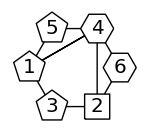

```mathematica
Show[Graphics[{Line[{q[1],q[2],q[3],q[4],q[5],q[6],q[1],q[3],q[1],q[5]}],
h[q[1][[1]],q[1][[2]],4],
p[q[2][[1]],q[2][[2]],5],
p[q[3][[1]],q[3][[2]],1],
p[q[4][[1]],q[4][[2]],3],
s[q[5][[1]],q[5][[2]],2],
h[q[6][[1]],q[6][[2]],6]}],AspectRatio->Automatic,ImageSize->150]
```

```mathematica
q[n_]:=.8{Cos[n 2Pi/5+Pi/10],Sin[n 2Pi/5+Pi/10]};
```

```mathematica
Show[Graphics[{Line[{q[2],q[3],q[4],q[5],q[1],q[2],q[5]}],
h[q[1][[1]],q[1][[2]],9],
h[q[2][[1]],q[2][[2]],2],
h[q[3][[1]],q[3][[2]],6],
t[q[4][[1]],q[4][[2]],4],
t[q[5][[1]],q[5][[2]],7]}],AspectRatio->Automatic,ImageSize->125]
```

-Graphics-

```mathematica
Show[Graphics[{Line[{q[2],q[3],q[4],q[5],q[1],q[2],q[5]}],
t[q[1][[1]],q[1][[2]],1],
p[q[2][[1]],q[2][[2]],7],
t[q[3][[1]],q[3][[2]],4],
h[q[4][[1]],q[4][[2]],6],
s[q[5][[1]],q[5][[2]],2]}],AspectRatio->Automatic,ImageSize->125]
```

-Graphics-

```mathematica
Show[Graphics[{Line[{q[2],q[3],q[4],q[5],q[1],q[2],q[5]}],
p[q[1][[1]],q[1][[2]],3],
p[q[2][[1]],q[2][[2]],1],
h[q[3][[1]],q[3][[2]],9],
s[q[4][[1]],q[4][[2]],8],
t[q[5][[1]],q[5][[2]],2]}],AspectRatio->Automatic,ImageSize->125]
```

-Graphics-

```mathematica
Show[Graphics[{Line[{q[2],q[3],q[4],q[5],q[1],q[2],q[5]}],
p[q[1][[1]],q[1][[2]],1],
p[q[2][[1]],q[2][[2]],7],
s[q[3][[1]],q[3][[2]],2],
h[q[4][[1]],q[4][[2]],6],
h[q[5][[1]],q[5][[2]],4]}],AspectRatio->Automatic,ImageSize->125]
```

-Graphics-

```mathematica
Show[Graphics[{Line[{q[2],q[3],q[4],q[5],q[1],q[2],q[5]}],
t[q[1][[1]],q[1][[2]],1],
p[q[2][[1]],q[2][[2]],6],
t[q[3][[1]],q[3][[2]],3],
p[q[4][[1]],q[4][[2]],5],
h[q[5][[1]],q[5][[2]],2]}],AspectRatio->Automatic,ImageSize->125]
```

-Graphics-

```mathematica
Show[Graphics[{Line[{q[2],q[3],q[4],q[5],q[1],q[2],q[5]}],
t[q[1][[1]],q[1][[2]],2],
h[q[2][[1]],q[2][[2]],7],
p[q[3][[1]],q[3][[2]],1],
h[q[4][[1]],q[4][[2]],5],
h[q[5][[1]],q[5][[2]],4]}],AspectRatio->Automatic,ImageSize->125]
```

-Graphics-

```mathematica
Show[Graphics[{Line[{q[2],q[3],q[4],q[5],q[1],q[2],q[5]}],
t[q[1][[1]],q[1][[2]],3],
s[q[2][[1]],q[2][[2]],4],
p[q[3][[1]],q[3][[2]],1],
h[q[4][[1]],q[4][[2]],9],
s[q[5][[1]],q[5][[2]],8]}],AspectRatio->Automatic,ImageSize->125]
```

-Graphics-

```mathematica
Show[Graphics[{Line[{q[2],q[3],q[4],q[5],q[1],q[2],q[5]}],
h[q[1][[1]],q[1][[2]],3],
h[q[2][[1]],q[2][[2]],4],
h[q[3][[1]],q[3][[2]],2],
s[q[4][[1]],q[4][[2]],8],
t[q[5][[1]],q[5][[2]],9]}],AspectRatio->Automatic,ImageSize->125]
```

-Graphics-

```mathematica
Show[Graphics[{Line[{q[2],q[3],q[4],q[5],q[1],q[2],q[5]}],
s[q[1][[1]],q[1][[2]],6],
p[q[2][[1]],q[2][[2]],2],
p[q[3][[1]],q[3][[2]],9],
h[q[4][[1]],q[4][[2]],7],
t[q[5][[1]],q[5][[2]],8]}],AspectRatio->Automatic,ImageSize->125]
```

-Graphics-

```mathematica
Show[Graphics[{Line[{q[2],q[3],q[4],q[5],q[1],q[2],q[5]}],
s[q[1][[1]],q[1][[2]],4],
h[q[2][[1]],q[2][[2]],3],
p[q[3][[1]],q[3][[2]],1],
p[q[4][[1]],q[4][[2]],9],
s[q[5][[1]],q[5][[2]],8]}],AspectRatio->Automatic,ImageSize->125]
```

-Graphics-

```mathematica
Show[Graphics[{Line[{q[3],q[4],q[5],q[1],q[2],q[3],q[1],q[4]}],
p[q[1][[1]],q[1][[2]],2],
p[q[2][[1]],q[2][[2]],9],
t[q[3][[1]],q[3][[2]],7],
s[q[4][[1]],q[4][[2]],4],
h[q[5][[1]],q[5][[2]],6]}],AspectRatio->Automatic,ImageSize->125]
```

-Graphics-

```mathematica
Show[Graphics[{Line[{q[3],q[4],q[5],q[1],q[2],q[3],q[1],q[4]}],
h[q[1][[1]],q[1][[2]],4],
p[q[2][[1]],q[2][[2]],6],
t[q[3][[1]],q[3][[2]],2],
p[q[4][[1]],q[4][[2]],1],
p[q[5][[1]],q[5][[2]],5]}],AspectRatio->Automatic,ImageSize->125]
```

-Graphics-

```mathematica
Show[Graphics[{Line[{q[3],q[4],q[5],q[1],q[2],q[3],q[1],q[4]}],
h[q[1][[1]],q[1][[2]],9],
h[q[2][[1]],q[2][[2]],4],
h[q[3][[1]],q[3][[2]],5],
h[q[4][[1]],q[4][[2]],2],
s[q[5][[1]],q[5][[2]],8]}],AspectRatio->Automatic,ImageSize->125]
```

-Graphics-

```mathematica
Show[Graphics[{Line[{q[3],q[4],q[5],q[1],q[2],q[3],q[1],q[4]}],
h[q[1][[1]],q[1][[2]],7],
h[q[2][[1]],q[2][[2]],2],
h[q[3][[1]],q[3][[2]],5],
h[q[4][[1]],q[4][[2]],6],
t[q[5][[1]],q[5][[2]],4]}],AspectRatio->Automatic,ImageSize->125]
```

-Graphics-

```mathematica
Show[Graphics[{Line[{q[3],q[4],q[5],q[1],q[2],q[3],q[1],q[4]}],
t[q[1][[1]],q[1][[2]],7],
p[q[2][[1]],q[2][[2]],9],
t[q[3][[1]],q[3][[2]],2],
s[q[4][[1]],q[4][[2]],4],
h[q[5][[1]],q[5][[2]],1]}],AspectRatio->Automatic,ImageSize->125]
```

-Graphics-

```mathematica
Show[Graphics[{Line[{q[3],q[4],q[5],q[1],q[2],q[3],q[1],q[4]}],
t[q[1][[1]],q[1][[2]],4],
t[q[2][[1]],q[2][[2]],3],
p[q[3][[1]],q[3][[2]],9],
t[q[4][[1]],q[4][[2]],2],
t[q[5][[1]],q[5][[2]],8]}],AspectRatio->Automatic,ImageSize->125]
```

-Graphics-

```mathematica
Show[Graphics[{Line[{q[3],q[4],q[5],q[1],q[2],q[3],q[1],q[4]}],
s[q[1][[1]],q[1][[2]],6],
p[q[2][[1]],q[2][[2]],9],
h[q[3][[1]],q[3][[2]],3],
s[q[4][[1]],q[4][[2]],8],
p[q[5][[1]],q[5][[2]],1]}],AspectRatio->Automatic,ImageSize->125]
```

-Graphics-

```mathematica
Show[Graphics[{Line[{q[3],q[4],q[5],q[1],q[2],q[3],q[1],q[4]}],
s[q[1][[1]],q[1][[2]],4],
h[q[2][[1]],q[2][[2]],6],
t[q[3][[1]],q[3][[2]],2],
p[q[4][[1]],q[4][[2]],9],
h[q[5][[1]],q[5][[2]],3]}],AspectRatio->Automatic,ImageSize->125]
```

-Graphics-

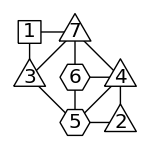

```mathematica
Show[Graphics[{Line[{{0,1},{1,2},{0,2},{0,1},{1,0},{2,0},{2,1},{1,0},{1,2},{2,1},{1,1}}],
t[0,1,3],
s[0,2,1],
t[1,2,7],
h[1,1,6],
h[1,0,5],
t[2,1,4],
t[2,0,2]}],AspectRatio->Automatic,ImageSize->150]
```